```mathematica
Quit[]
```

```mathematica
<<BBHpnToolkit`
```

Authors: Rickmoy Samanta(rickmoysamanta@gmail.com); Sashwat Tanay (sashwattanay@gmail.com, https://sashwattanay.github.io/sashwat_site/)

```mathematica
(*User input*)
m1=5/2  ;            (*bigger mass*)
m2=1    ;              (*smaller mass*)
(*G=1; μ= (m1 m2)/(m1+m2); M=m1+m2;*)

ϵ=3./1000           (* This is 1/c^2 *);
R=2{ 1,1,1};

P={1/2 ,-1/2,1/3};
(*L=Norm[ Cross[R,P]]*)
S1={0,1,1}√ϵ  ;              S2={1,-3/10,0}√ϵ;   

(*S1 and S2 (with √ϵ included) are the spin angular momenta of the two black holes. Their dimension is same as that of orbital angular momentum L = R x P. *)
```

```mathematica
(*eng=(Norm[P])^2/(2 μ)-(G M μ)/Norm[R]*)
```

# parameter estimates

```mathematica
eng= frequency[m1,m2,R,P,S1,S2,ϵ][[1]]
pnparam=(Norm[P]/(m1 m2/(m1+m2)))^2 ϵ
Gc=1; a=(-Gc  m1 m2)/(2 eng);
tp=2 π( a^3/(Gc (m1+m2)))^(1/2)
tp/(pnparam)^1
```

-0.297117

0.00359333

28.9814

8065.31

# Frequencies

```mathematica
freqArr= frequency[m1,m2,R,P,S1,S2,ϵ][[2]]            (*The 5 frequencies (within the action-angle framework) of the system*)
```

{0.000102314,0.,0.214619,0.214141,0.000127328}

# BBH system at a later time

```mathematica
(*State of the system at time = tf. We are giving {R,P,S1,S2}*)        

NmHflow[m1,m2,R,P,S1,S2,tf  ,ϵ]                   (*got via numerical integration of Hamilton's equations*)  
Acflow[m1,m2,R,P,S1,S2,tf  ,ϵ]
(*got from the action-angle-based closed-form solution as given in arXiv:2110.15351 and arXiv:2012.06586 *)
                     
Hflow[m1,m2,R,P,S1,S2,tf  ,ϵ]     
(*got from the closed-form solution via integrating the Hamilton's equations as in arXiv:1908.02927 (with 1PN effects added)*)
```

{{1.67774,-1.51449,2.42094},{-0.200104,-0.621825,-0.108027},{0.00352294,0.0235455,0.0378576},{0.0257887,-0.020055,-0.00476897}}

{{1.70694,-1.46638,2.44642},{-0.194486,-0.621617,-0.101115},{0.00352368,0.0235463,0.0378571},{0.0257582,-0.0200519,-0.0048062}}

{{1.70694,-1.46638,2.44642},{-0.194486,-0.621617,-0.101114},{0.00352369,0.0235463,0.0378571},{0.0257582,-0.0200519,-0.0048062}}

# error computation

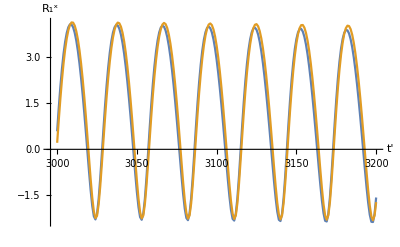

```mathematica
ListLinePlot[{Table[{t,NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]][[1]]},{t,3000,3200,1}],Table[{t,Hflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]][[1]]},{t,3000,3200,1}]},(*PlotStyle->{Blue,Red},*)AxesLabel->{Style["t'",Black,FontFamily->"Candara",FontSize->30],Style["R_1^x",Black,FontFamily->"Cambria",FontSize->30]},TicksStyle->Directive[Lighter[Black],FontSize->14](*,PlotLegends->Placed[{"Numerical","Analytical"},{.5,1}]*)]
```

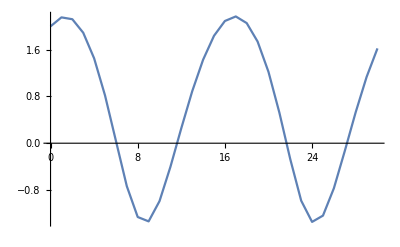

```mathematica
ListLinePlot[Table[{t,NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]][[1]]},{t,0,30,1}]]
```

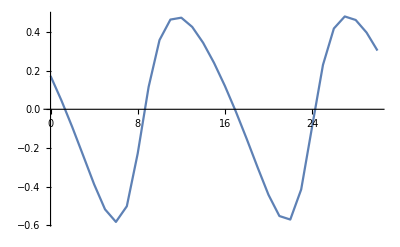

```mathematica
ListLinePlot[Table[{t,NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[2]][[1]]},{t,0,30,1}]]
```

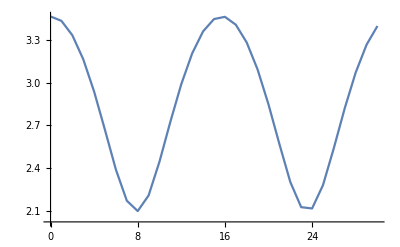

```mathematica
ListLinePlot[Table[{t,Norm[NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]]]},{t,0,30,1}]]
```

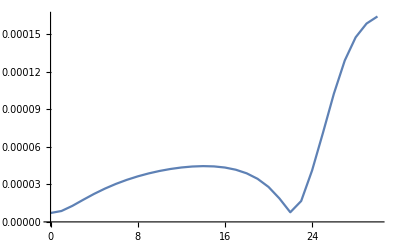

```mathematica
ListLinePlot[Table[{t,VectorAngle[NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]],Acflow[m1,m2,R,P,S1,S2,t  ,ϵ][[1]]]},{t,0,30,1}]]
```

```mathematica
VectorAngle[NmHflow[m1,m2,R,P,S1,S2,5 ,ϵ][[1]],Acflow[m1,m2,R,P,S1,S2,5  ,ϵ][[1]]]
```

0.000026661

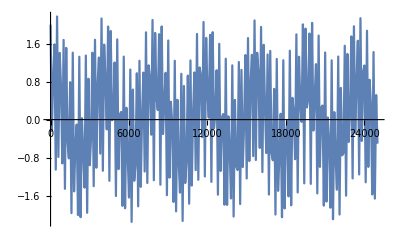

```mathematica
(*ϵ=1./1000 ;*)ListLinePlot[Table[{t,NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]][[1]]},{t,0,25000,100}]]
```

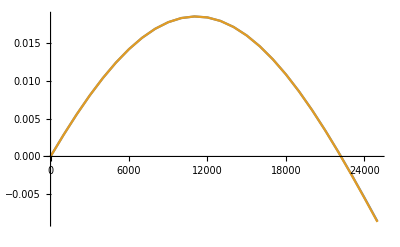

```mathematica
ListLinePlot[{Table[{t,NmHflow[m1,m2,R,P,S1,S2,t ,ϵ][[3]][[1]]},{t,0,25000,1000}],Table[{t,Hflow[m1,m2,R,P,S1,S2,t ,ϵ][[3]][[1]]},{t,0,25000,1000}]}]
```

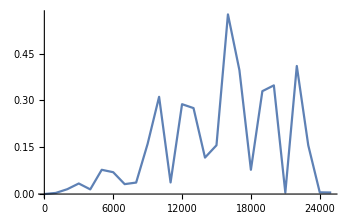

```mathematica
ListLinePlot[Table[{t,Abs[1-Norm[Acflow[m1,m2,R,P,S1,S2,t ,ϵ][[1]]]/Norm[NmHflow[m1,m2,R,P,S1,S2,t  ,ϵ][[1]]]]},{t,0,25000,1000}]]
```